```mathematica
SetDirectory["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone"];
PureIntegralsNEW=ReadList[FileNameJoin[{Directory[],"files/PureIntegralBasis1-151.txt"}]];
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
$P=2^31-1;
```

```mathematica
PureIntegralsNEW[[152;;]]//Length
ReduListT=PureIntegralsNEW[[152;;]]/.hxb[n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_,n9_,n10_,n11_,n12_,n13_]:>{n1,n2,n3,n4,n5,n6,n7,n8,n9,n10,n11,n12,n13};
Sectors=ReduListT/.( n_Integer:>0/;n<0)/.( n_Integer:>1/;n>1) //DeleteDuplicates;
Sectors2=ReduListT/.( n_Integer:>0/;n<0)/.( n_Integer:>1/;n>1) ;
RemainingSectors=SortBy[Tally[Sectors2],Last]
RemainingSectors//Length
```

90

{{{0,1,1,1,0,1,1,1,1,0,0,0,0},1},{{1,0,1,1,0,0,1,1,1,0,0,0,0},1},{{1,0,1,1,0,1,0,1,1,0,0,0,0},1},{{1,0,1,1,0,1,1,1,1,0,0,0,0},1},{{1,0,1,1,1,0,1,1,0,0,0,0,0},1},{{1,0,1,1,1,1,0,1,0,0,0,0,0},1},{{1,0,1,1,1,1,1,1,0,0,0,0,0},1},{{1,1,0,1,1,1,1,1,0,0,0,0,0},1},{{1,1,1,1,1,1,1,1,1,0,0,0,0},1},{{0,1,1,1,0,0,1,1,0,0,0,0,0},2},{{0,1,1,1,0,0,1,1,1,0,0,0,0},2},{{0,1,1,1,0,1,0,1,0,0,0,0,0},2},{{0,1,1,1,0,1,0,1,1,0,0,0,0},2},{{0,1,1,1,0,1,1,1,0,0,0,0,0},2},{{1,1,0,1,0,1,0,1,0,0,0,0,0},2},{{1,1,0,1,0,1,1,1,0,0,0,0,0},2},{{1,1,0,1,1,0,1,1,0,0,0,0,0},2},{{1,1,0,1,1,1,0,1,0,0,0,0,0},2},{{1,1,1,1,0,1,1,1,1,0,0,0,0},3},{{1,1,1,1,1,0,1,1,1,0,0,0,0},3},{{1,1,1,1,1,1,0,1,0,0,0,0,0},3},{{1,1,1,1,1,1,0,1,1,0,0,0,0},3},{{1,1,1,1,1,1,1,1,0,0,0,0,0},3},{{1,1,1,1,0,0,1,1,1,0,0,0,0},4},{{1,1,1,1,0,1,0,1,1,0,0,0,0},4},{{1,1,1,1,1,0,1,1,0,0,0,0,0},4},{{1,1,1,1,0,0,1,1,0,0,0,0,0},5},{{1,0,1,1,0,0,1,1,0,0,0,0,0},6},{{1,0,1,1,0,1,0,1,0,0,0,0,0},6},{{1,0,1,1,0,1,1,1,0,0,0,0,0},6},{{1,1,1,1,0,1,0,1,0,0,0,0,0},6},{{1,1,1,1,0,1,1,1,0,0,0,0,0},7}}

32

```mathematica
Position[Sectors2/.{n1_,n2_,n3_,n4_,n5_,n6_,n7_,n8_,n9_,n10_,n11_,n12_,n13_}:>hxb[n1,n2,n3,n4,n5,n6,n7,n8,n9,n10,n11,n12,n13],RemainingSectors[[19,1]]/.List->hxb]+119
```

{{123},{141}}

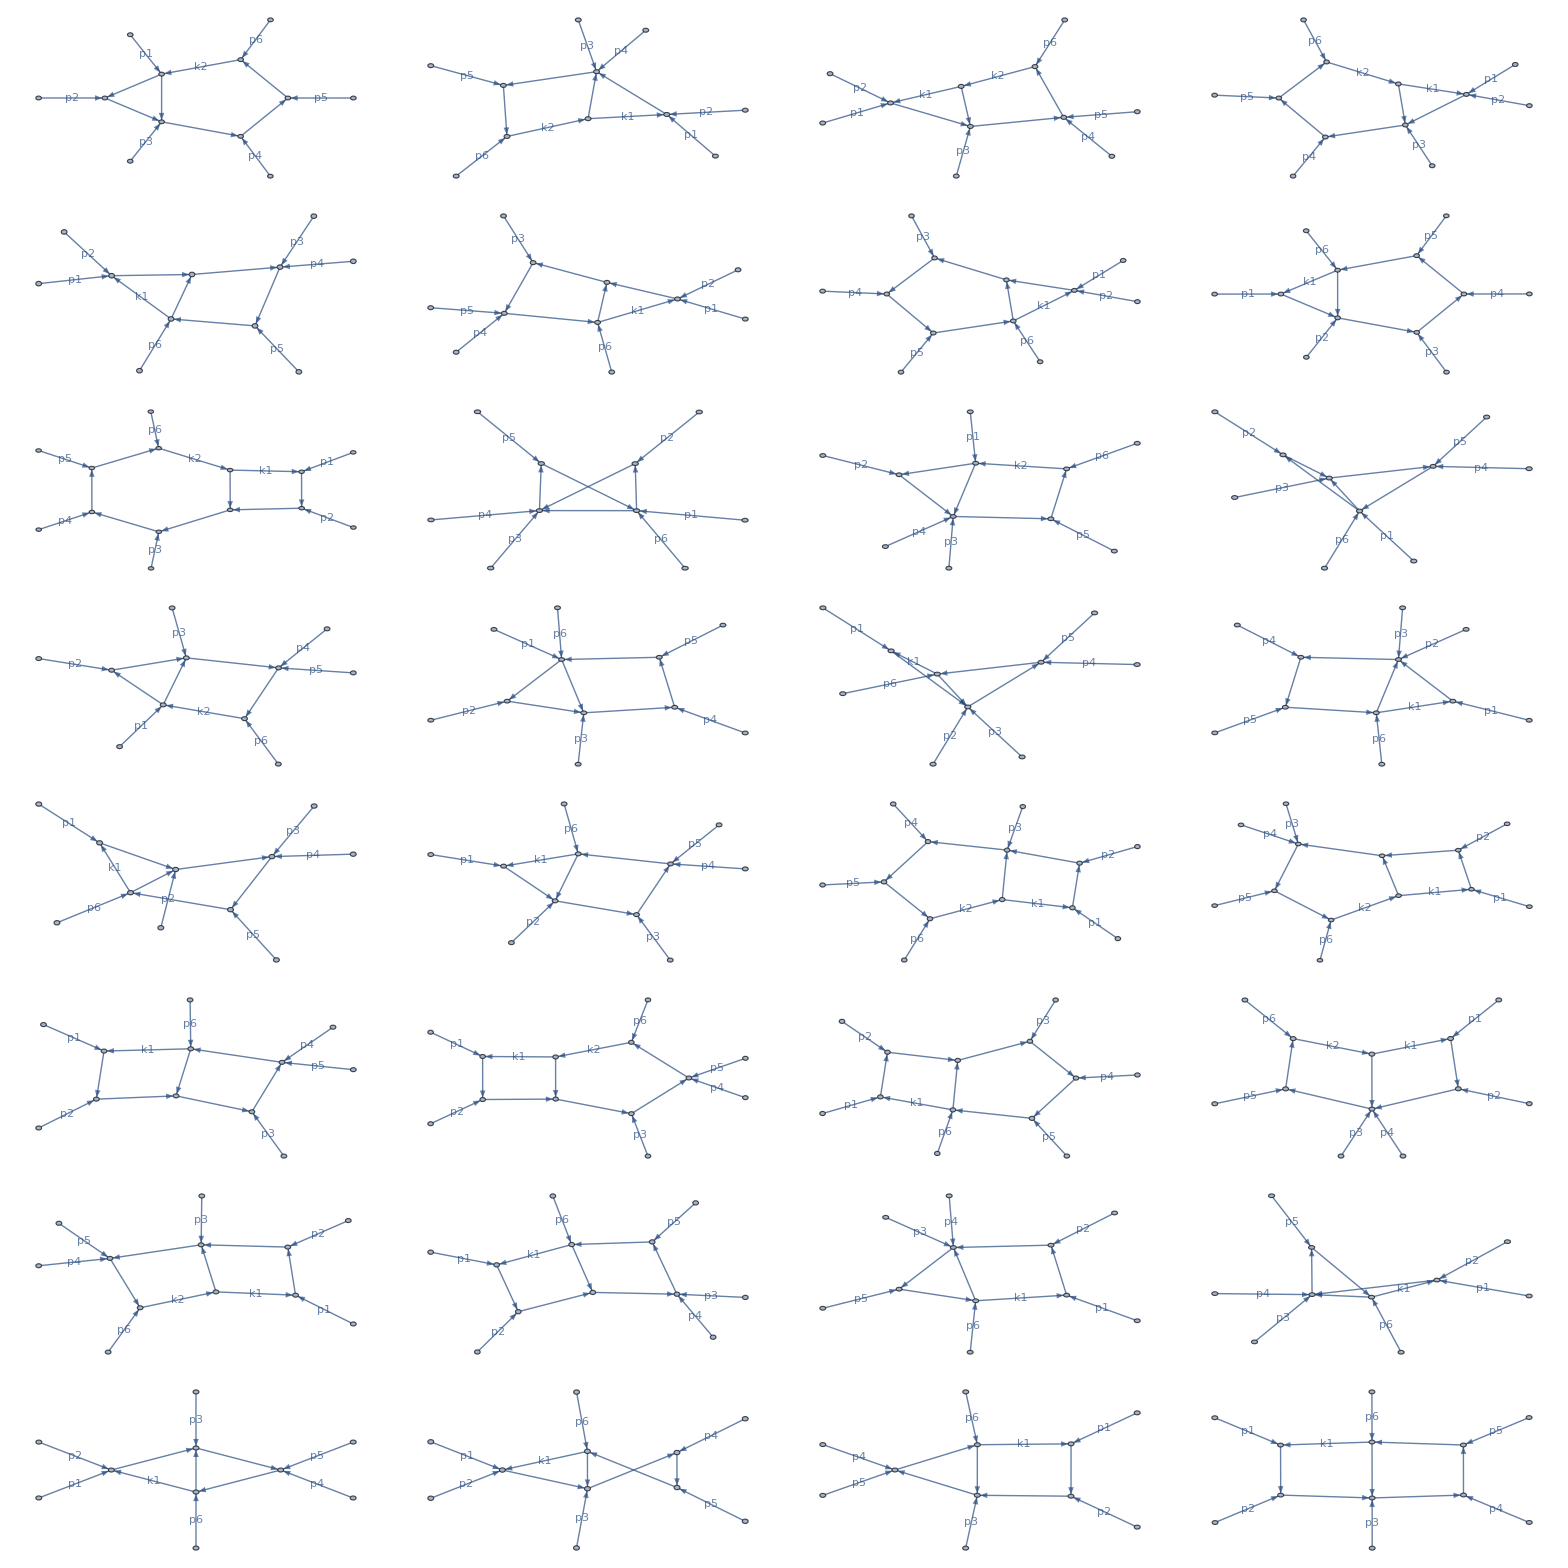

```mathematica
PlotDiagrams=Table[plotDiagram[RemainingSectors[[i,1]]],{i,1,Length[RemainingSectors]}];
Grid[ArrayReshape[PlotDiagrams,{8,4}]]
```

```mathematica
17*3
```

51

(2 | 2
2 | 2
2 | 2
1 | 0)

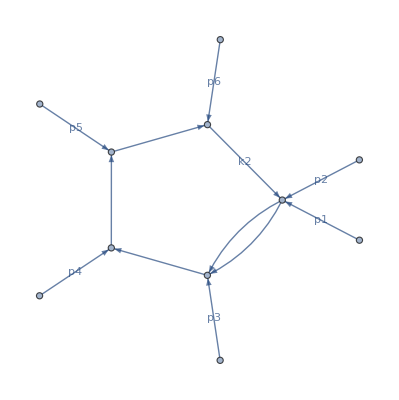
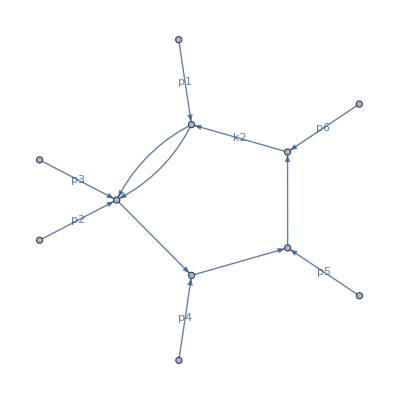
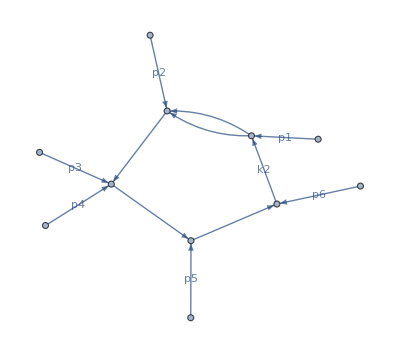
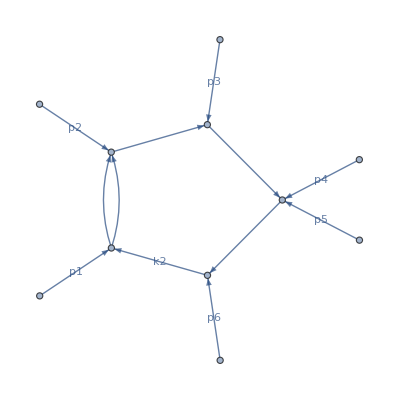
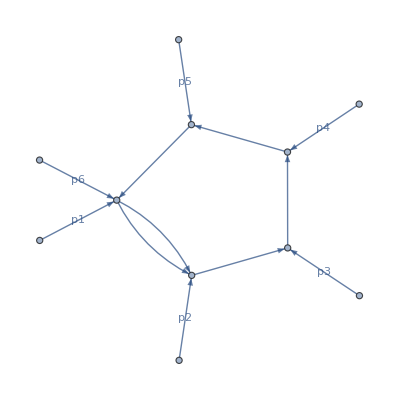
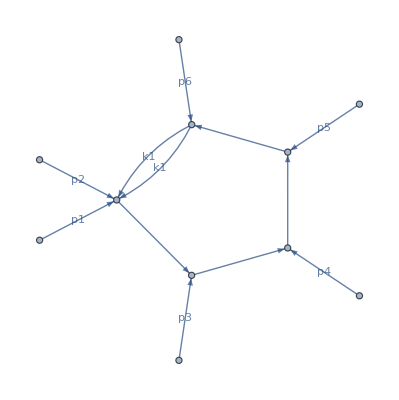
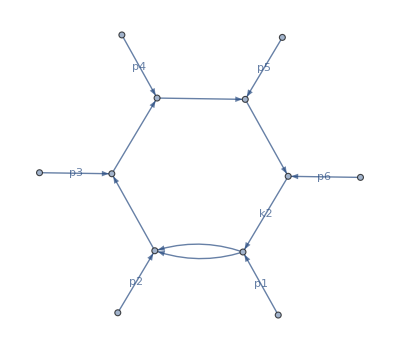
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | 0

```mathematica
RemSubBubbles={11,12,13,14,15,21,1};
ArrayReshape[RemainingSectors[[RemSubBubbles]][[All,2]],{4,2}]//MatrixForm
Grid[ArrayReshape[PlotDiagrams[[RemSubBubbles]],{4,2}]]
```

Cycles[{{1,19,28,4,20,29,5,8,22,30,17,14,12,2,6,9,32,27,16,13,11,10},{3,7,21,23,31,18,15}}]

{10,12,15,28,29,2,3,5,6,11,13,14,16,17,18,27,30,31,1,4,7,8,21,24,25,26,32,19,20,22,23,9}

(2 | 2 | 2 | 6
6 | 1 | 1 | 1
1 | 2 | 2 | 2
2 | 2 | 2 | 5
6 | 6 | 1 | 1
1 | 1 | 3 | 4
4 | 4 | 7 | 3
3 | 3 | 3 | 1)

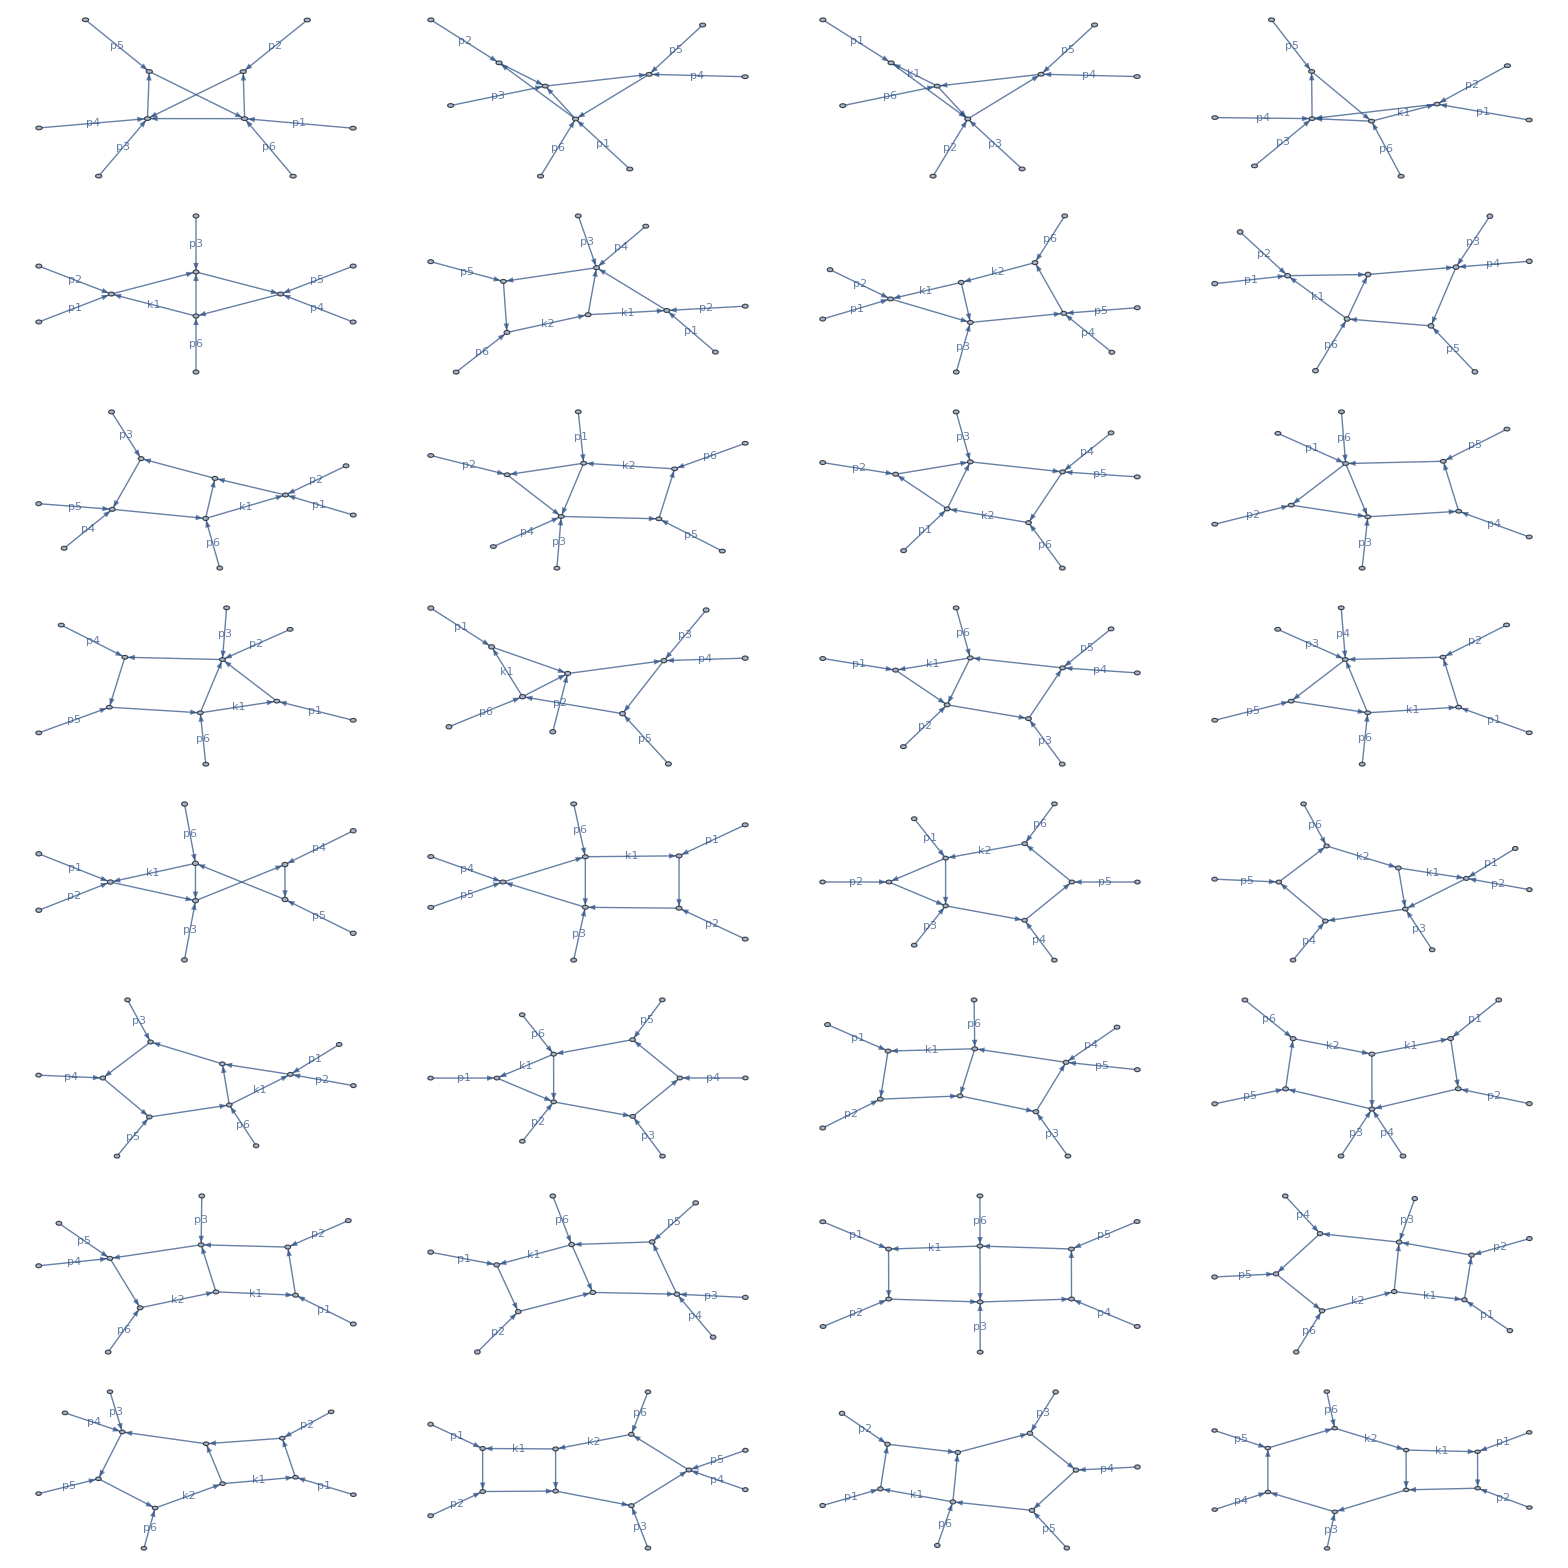

```mathematica
Form=Thread[Total[Transpose[RemainingSectors[[All,1]]]]]-1;
Permutation=FindPermutation[Form,Sort[Form]]
RemNEw=Permute[Range[1,32],Permutation]
ArrayReshape[RemainingSectors[[RemNEw]][[All,2]],{8,4}]//MatrixForm
Grid[ArrayReshape[PlotDiagrams[[RemNEw]],{8,4}]]
```

```mathematica
RemainingSectors[[RemNEw]][[1,1]]
RemainingSectors[[RemNEw]][[2,1]]
RemainingSectors[[RemNEw]][[3,1]]
```

{0,1,1,1,0,0,1,1,0,0,0,0,0}

{0,1,1,1,0,1,0,1,0,0,0,0,0}

{1,1,0,1,0,1,0,1,0,0,0,0,0}

```mathematica
Length[RemainingSectors]
```

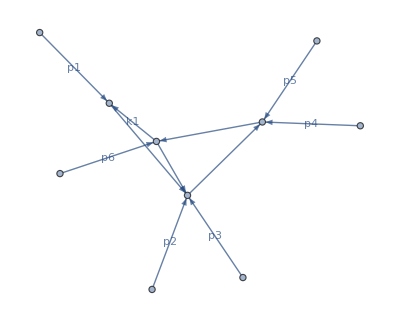

```mathematica
plotDiagram[{1,1,0,1,0,1,0,1,0,0,0,0,0}]
```